```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/LYE/GDC_Conf_AR_LYE_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/LYE/GDC_Conf_BR_LYE_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojCHEVBKAR=confAR[[All,1]][[All,1]]
dojCHAR=confAR[[All,2]][[All,3]]
dojEVBKAR=confAR[[All,3]][[All,3]]

dojCHEVBKBR=confBR[[All,1]][[All,1]]
dojCHBR=confBR[[All,2]][[All,3]]
dojEVBKBR=confBR[[All,3]][[All,3]]
```

{0.00121095,0.00121095,0.00526316,0.00625,0.00543478,0.0222222,1.,1.}

{0.00109016,0.00103105,0.00111718,0.0010752,0.000612063,0.000342354,0.000451474,0.000435964}

{0.000165487,0.0000312663,8.36213×10^-7,3.43271×10^-8,2.64574×10^-9,6.58731×10^-11,2.14577×10^-13,9.9865×10^-14}

{0.00121095,0.00121095,0.00526316,0.00383142,0.0021322,0.0222222,DOJ ist nicht definiert! Division durch Null! }

{0.00103105,0.000990076,0.0010752,0.000612063,0.000342354,0.000338286,0.000435964}

{0.00025013,0.0000181722,4.07634×10^-8,3.75293×10^-9,6.86544×10^-10,9.65596×10^-12,0.}

```mathematica
(*sList={"S0","S1","S2","S3","S4","S5","S6","S7","S8"};
dojP=Labeled[#[[1]],#[[2]]]&/@Map[{doj[[#]],sList[[#]]}&,ran]*)

sList={1,2,3,4,5,6,7,8};
sList2={1.5,2.5,3.5,4.5,5.5,6.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojAAR={#[[2]],#[[1]]}&/@Map[{N[dojCHAR[[#]]/dojCHEVBKAR[[#]]],sList[[#]]}&,ran]
dojABR={#[[2]],#[[1]]}&/@Map[{N[dojCHBR[[#]]/dojCHEVBKBR[[#]]],sList2[[#]]}&,ran2]
dojPCHAR={#[[2]],#[[1]]}&/@Map[{dojCHAR[[#]],sList[[#]]}&,ran]
dojPCHBR={#[[2]],#[[1]]}&/@Map[{dojCHBR[[#]],sList2[[#]]}&,ran2]
dojPEVBKAR={#[[2]],#[[1]]}&/@Map[{dojEVBKAR[[#]],sList[[#]]}&,ran]
dojPEVBKBR={#[[2]],#[[1]]}&/@Map[{dojEVBKBR[[#]],sList2[[#]]}&,ran2]
```

{{1,0.900251},{2,0.851443},{3,0.212264},{4,0.172032},{5,0.11262},{6,0.0154059},{7,0.000451474},{8,0.000435964}}

{{1.5,0.851443},{2.5,0.817605},{3.5,0.204288},{4.5,0.159749},{5.5,0.160564},{6.5,0.0152229}}

{{1,0.00109016},{2,0.00103105},{3,0.00111718},{4,0.0010752},{5,0.000612063},{6,0.000342354},{7,0.000451474},{8,0.000435964}}

{{1.5,0.00103105},{2.5,0.000990076},{3.5,0.0010752},{4.5,0.000612063},{5.5,0.000342354},{6.5,0.000338286}}

{{1,0.000165487},{2,0.0000312663},{3,8.36213×10^-7},{4,3.43271×10^-8},{5,2.64574×10^-9},{6,6.58731×10^-11},{7,2.14577×10^-13},{8,9.9865×10^-14}}

{{1.5,0.00025013},{2.5,0.0000181722},{3.5,4.07634×10^-8},{4.5,3.75293×10^-9},{5.5,6.86544×10^-10},{6.5,9.65596×10^-12}}

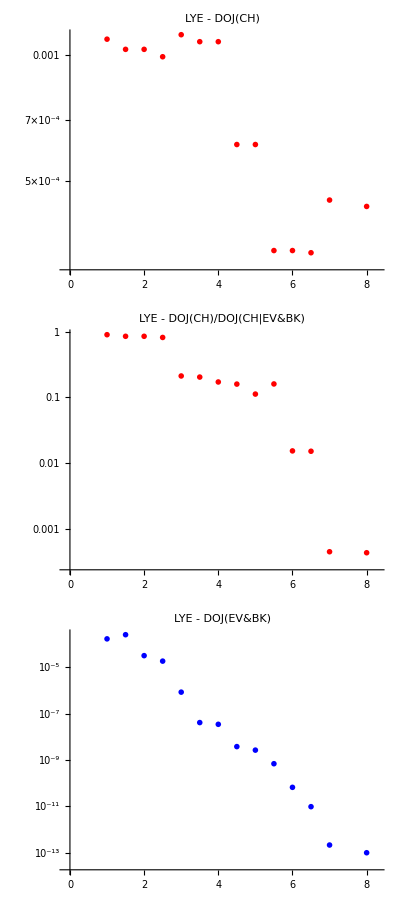

```mathematica
aPlot=ListLogPlot[{Union[dojAAR,dojABR]},  PlotLabel->"LYE - DOJ(CH)/DOJ(CH|EV&BK)", PlotRange->{{-0.1,8.3},All}, PlotStyle-> {Red}, PlotRange->All, PlotMarkers->{{"A",12}},ImageSize->400];
chPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR]},PlotRange->{{-0.1,8.3},All}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"LYE - DOJ(CH)", PlotMarkers->{{"C",12}},ImageSize->400];
evbkPlot=ListLogPlot[{Union[dojPEVBKAR,dojPEVBKBR]},  PlotRange->{{-0.1,8.3},All}, PlotStyle-> {Blue}, PlotRange->All, PlotLabel->"LYE - DOJ(EV&BK)", PlotMarkers->{{"E",12}},ImageSize->400];
allPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR], Union[dojPEVBKAR,dojPEVBKBR]}, PlotLegends->{"DOJ(CH)","DOJ(EV&BK)"}, PlotRange->{{-0.1,8.3},All}, PlotStyle-> {Red, Blue}, PlotRange->All, PlotLabel->"LYE - DOJ(CH),DOJ(EV&BK)", PlotMarkers->{{"C",12},{"E",12}},ImageSize->400];
plotsOut=Column[{chPlot,aPlot,evbkPlot}, ItemSize->35, Alignment->Center]
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/LYE/"];
Export["LYE_CH_EVBK.jpeg",plotsOut,ImageResolution->200]
Put[Union[dojPCHAR,dojPCHBR],"LYE_Z_APP.txt"]
Put[Union[dojAAR,dojABR],"LYE_F_APP.txt"]
```

LYE_CH_EVBK.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.026},  PlotLabel->"LYE - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["LYE_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```